```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* constantes fisicas *)
Clear[hbar,e,massae,eps0]
hbar=1.0545718 10^-34;(* constante de Planck *)
e=1.6021766 10^-19 ;(* carga do eletron *)
massae=9.10938356 10^-31 ;(* masa do eletron *)
eps0=8.8541878176 10^-12;(* constante de permissividade do vácuo *)
```

```mathematica
Clear[deltaEc,deltaEv,me,mh,ctedielet,camadas,a]
(* os seguintes dados são para nanocristais de Perovskita *)
deltaEc=1.25e; (* altura do poco do eletron *)
deltaEv=1.45e; (* altura do poco do buraco *)
me=massae.15 ;(* massa efetiva do eletron *)
mh=massae.14 ;(* massa efetiva do buraco *)
ctedielet=4.96; (* cte dieletrica *)
camadas=26; (* numero de camadas *)
a=camadas.59 10^-9;(* largura do nanocubo *)
Print[a]
```

1.534×10^-8

```mathematica
Clear[mi,eps]
(* outras constântes *)
mi=1/(1/me+1/mh); (* mu_perp *)
eps=ctedielet eps0; (* permissividade do material *)
```

```mathematica
Clear[keFunc,kappaeFunc,fTranscEFunc,EchuteE,khFunc,kappahFunc,fTranscHFunc,EchuteH]
keFunc[energia_]:=Sqrt[2me energia]/hbar(* função k do elétron *)
kappaeFunc[energia_]:=Sqrt[2me(deltaEc-energia)]/hbar(* função kappa do elétron *)
fTranscEFunc[energia_]:=keFunc[energia]Tan[keFunc[energia]a/2]-kappaeFunc[energia] (* eq. transcendental do elétron *)
EchuteE[]:=(For[Ei=0,Ei<deltaEc,Ei+=deltaEc/1000,
If[fTranscEFunc[Ei]fTranscEFunc[Ei+deltaEc/1000 ]<0,Break[]]
];
Return[Ei])(* retorna um valor aproximado para o valor de energia correspondente a primeira raiz de fTranscEFunc *)
khFunc[energia_]:=Sqrt[2mh energia]/hbar(* função k do buraco *)
kappahFunc[energia_]:=Sqrt[2mh(deltaEv-energia)]/hbar(* função kappa do buraco *)
fTranscHFunc[energia_]:=khFunc[energia]Tan[khFunc[energia]a/2]-kappahFunc[energia] (* eq. transcendental do buraco *)
EchuteH[]:=(For[Ei=0,Ei<deltaEv,Ei+=deltaEv/1000,
If[fTranscHFunc[Ei]fTranscHFunc[Ei+deltaEv/1000 ]<0,Break[]]
];
Return[Ei])(* retorna um valor aproximado para o valor de energia correspondente a primeira raiz de fTranscHFunc *)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

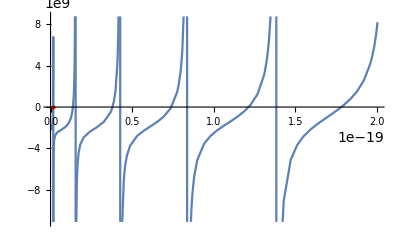

```mathematica
Clear[Ee,ke,kappae]
Ee=energia/.FindRoot[fTranscEFunc[energia],{energia,EchuteE[]}];
ke=keFunc[Ee];
kappae=kappaeFunc[Ee];

Show[Plot[fTranscEFunc[energia],{energia,0,deltaEc}],Graphics[{PointSize[Medium],Red,Point[{Ee,0}]}]]
```

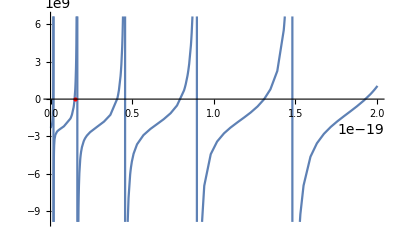

```mathematica
Clear[Eh,kh,kappah]
Eh=energia/.FindRoot[fTranscHFunc[energia],{energia,EchuteH[]}];
kh=khFunc[Eh];
kappah=kappahFunc[Eh];

Show[Plot[fTranscHFunc[energia],{energia,0,deltaEc}],Graphics[{PointSize[Medium],Red,Point[{Eh,0}]}]]
```

```mathematica
(* tamanho do infinito para a variavel a e "dobro do infinito" para x.
Esse ponto é escolhido como sendo o ponto em que a função de onda do elétron tem valor 10^-3 *)
L=2Log[Cos[ke a/2]Exp[kappae a/2]10^3]/kappae;
```

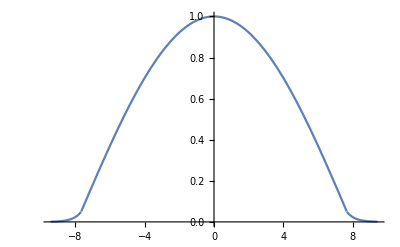

```mathematica
Clear[psie]
(* funcao de onda do elétron em função da distância x *)
psie[x_]=Piecewise[{{Cos[ke a/2]Exp[kappae a/2]Exp[kappae x],x<-a/2},{Cos[ke x],Abs[x]<a/2},{Cos[ke a/2]Exp[kappae a/2]Exp[-kappae x],x>a/2}}];
Plot[psie[x],{x,-L/2,L/2}]
```

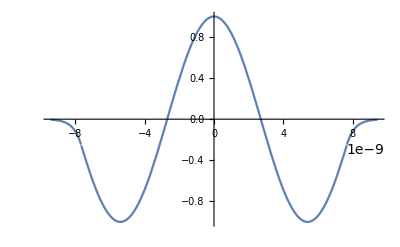

```mathematica
Clear[psih]
(* funcao de onda do buraco em função da distância x *)
psih[x_]=Piecewise[{{Cos[kh a/2]Exp[kappah a/2]Exp[kappah x],x<-a/2},{Cos[kh x],Abs[x]<a/2},{Cos[kh a/2]Exp[kappah a/2]Exp[-kappah x],x>a/2}}];
Plot[psih[x],{x,-L/2,L/2}]
```

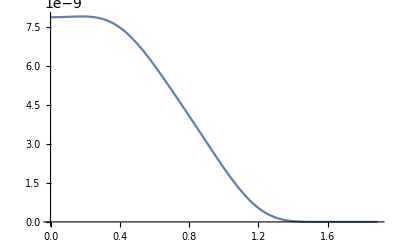

```mathematica
Clear[pInte,pAux,p]
pAux[a_]:=NIntegrate[(psie[z+a]psih[z])^2+(psie[z]psih[z+a])^2,{z,-L/2,L/2-a}]
p=Interpolation[Table[{a,pAux[a]},{a,0,L,L/100}]];
Plot[p[a],{a,0,L}]
```

```mathematica
Clear[d,A,B,c,EsAux,Es]
(* o ponto de mínimo é procurado em um range de lambda entre [lambIni, lambFin] com lambN pontos *)
lambIni=4. 10^-9;
lambFin=8. 10^-9;
lambN=10;
Es={};(* array das energias calculadas para cada valor de beta e lamb *)
Timing[
For[lamb=lambIni,lamb<=lambFin,lamb+=(lambFin-lambIni)/(lambN-1),
d=NIntegrate[p[x]p[y]p[z]Exp[-2/lamb Sqrt[x^2+y^2+z^2]],{x,0,L},{y,0,L},{z,0,L}];
A=Ee d+hbar^2/2/me/lamb^2 d;
B=Eh d+hbar^2/2/mh/lamb^2 d;
c=-e^2/4/Pi/eps NIntegrate[p[x]p[y]p[z]Exp[-2/lamb Sqrt[x^2+y^2+z^2]]/Sqrt[x^2+y^2+z^2],{x,0,L},{y,0,L},{z,0,L}];
Eb=((A+B+c)/d-Ee-Eh)/e/10^-3;
AppendTo[Es,Eb]
]][[1]]/60
valores={a 10^9,lambIni 10^9,lambFin 10^9,lambN};
out={valores};
For[i=1,i≤lambN,i++,AppendTo[out,Es[[i]]]]
nome="nanocubo_"<>ToString[a 10^9]<>".csv";
Export[nome,out];(* exporta um arquivo .csv do array "valores" na primeira linha e o array "Es" na segunda *)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.74896